# Bending of a Thin Plate

Classic plate theory calculations

Jorge Carabali Caicedo, Jun. 24,  2018

Plates are structural elements that has one of its dimension significantly lesser that the other two. Classic plate theory was first formulated by Kirchhoff; Under the assumption that straight lines perpendicular to the medium plane of plate remain perpendicular after the load is applied; The angular deformation on the planes perpendicular to the medium plane are negligible and the linear deformation in the perpendicular direction of the medium plane is negligible.

## Model Definition

-Graphics-

Considering a circular plate of radius r  with a constant pressure applied in one face. According to Plate Theory the general expression in  rectangular coordinates is written as follows:

2 (∂^4 w(x,y))/(∂x^2 ∂y^2)+(∂^4 w(x,y))/(∂x^4)+(∂^4 w(x,y))/(∂y^4)=P/D

Where : P is the pressure and D is a constant "Plate Constant" which depends upon the material properties, in this  essay P/D is going to be named as lowercase c. Since we already assumed that the deflection is small the deflection can be written as a function of r w[r].

Converting  general equation to Polar Coordinates :

Clears the variable c and R and converts the rectangular plate equation into  polar coordinates.

```mathematica
Clear[c,R]
eqn= Laplacian[Laplacian[w[r],{r,θ},"Polar"],{r,θ},"Polar"]== c
```

(2 w'[r])/r^3-(2 w''[r])/r^2+(w^(3)[r])/r+(-w'[r]/r^2+w''[r]/r+w^(3)[r])/r+w^(4)[r]==c

Once is converted can be simplified :

Simplifies the polar plate equation.

```mathematica
eqn=Simplify[eqn]
```

w''[r]+r (c r-2 w^(3)[r]-r w^(4)[r])==w'[r]/r

## Solving DE for boundary condition with fixed support at the center

A plate can be supported differently and depending on the type of support the boundary conditions change, consider a disk supported at the center.

For  r=0  ,   the equation transformed to polar coordinates is solved as follows:

Solves the polar coordinate equation for the plate with  the condition that the  deflection and deflection derivative are  equal to zero at the center (r=0)

```mathematica
sol=First@DSolve[{eqn,w[0]==0,w'[0]==0},w,r]
```

{w→Function[{r},1/64 (c r^4+32 r^2 C[2]-16 r^2 C[3]+32 r^2 C[3] Log[r])]}

Takes the solution and plugs it  into the deflection function.

```mathematica
ww[r_]=w[r]/.sol
```

1/64 (c r^4+32 r^2 C[2]-16 r^2 C[3]+32 r^2 C[3] Log[r])

Furthermore , all odd derivatives with respect to r in the center should be 0 :

Takes the second  derivative of the deflection function.

```mathematica
D[D[ww[r],r],r]
```

1/64 (12 c r^2+64 C[2]+64 C[3]+64 C[3] Log[r])

Note , that Log[r] for  r→ 0 becomes ∞ , then C[3] needs to be  0.

Evaluates the constant into the function.

```mathematica
ww[r_]=(ww[r]/.C[3]->0)
```

1/64 (c r^4+32 r^2 C[2])

Last but not least, when the radius is  equal to the total r = R . We can assume that there is no bending at the end and , thus, ww'[R]=0.

Solves the constraint  with the condition that the second derivative of the deflection must be zero at the end of the disk.

```mathematica
constraint=First@Solve[ww''[R]==0,C[2]]
```

{C[2]→-(3 c R^2)/16}

Finally  the bending equation can be obtained  which depends on c (pressure over plate constant) and the radius :

The constraint plugs into the final bending equation.

```mathematica
bend[c_,R_,r_]=(ww[r]/. constraint )
```

1/64 (c r^4-6 c r^2 R^2)

## Visualize the results

When the pressure is applied the  plate starts bending as show in the 2D plot, for different value of pressure  the bending increases.

Plot the  bending of  disk with a fixed support at the center, keeping the radius fixed  (1 unity) , and  the constant c increases from 0 to 1.

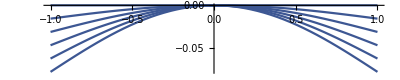

```mathematica
With[
{R=1},
Plot[Table[bend[c,R,r],{c,0,1,0.2}],{r,-R,R},AspectRatio->0.2,ColorFunction->(&)]
]
```

A 3D plot of the plate  after the pressure is applied  is shown afterwards :

Plot  the bending of the plate  keeping the radius and constant c fixed.

```mathematica
With[
{R=1,c=0.3},
RevolutionPlot3D[bend[c, R, r],{r,-R,R},ColorFunction->([#3]&)]
]
```

-Graphics3D-

The change of the constant c and the radius can be plotted  , in order to  see how they correlate.

Plot the  change of radius and the constant c.

```mathematica
With [ {R=1},Plot3D[{bend[c, R, r]/.R->1} ,{c,0,0.3},{r,0,R},ColorFunction->([#3]&)]]
```

-Graphics3D-

### Solving DE for boundary condition with fixed support at the ends

The result from above  can be used to  analyze different kind of supports, now consider a disk with fix supports at the end.

Solve the general equation  of plate theory in polar coordinates and clear the values relates to the deflection of this second case (ww2).

```mathematica
sol2=First@DSolve[{eqn},w,r]
ClearAll[ww2]
```

{w→Function[{r},(c r^4)/64+1/2 r^2 C[2]-1/4 r^2 C[3]+C[4]+C[1] Log[r]+1/2 r^2 C[3] Log[r]]}

Plugs the solution from above in a function  ww2, which depends on the radius.

```mathematica
ww2[r_]=w[r]/.sol2
```

(c r^4)/64+1/2 r^2 C[2]-1/4 r^2 C[3]+C[4]+C[1] Log[r]+1/2 r^2 C[3] Log[r]

From the equation  above  C[3] = 0 and C[1] = 0 , since as explained above these constant need to be zero  otherwise the deflection goes to infinity, which is not possible.

Plugs the constraints into the deflection equation  ww2.

```mathematica
ww2[r_]=(ww2[r]/.{C[3]->0, C[1]->0})
```

(c r^4)/64+1/2 r^2 C[2]+C[4]

Now the other constant are obtained.

Solves  the constraint  and store the result into the final bending equation  ( bendsecond).

```mathematica
constraint2=Solve[ww2'[R]==0 && ww2[R]==0,{C[2],C[4]}]
```

{{C[2]→-(c R^2)/16,C[4]→(c R^4)/64}}

```mathematica
bendsecond[r_,c_,R_]=(ww2[r]/.constraint2)
```

{(c r^4)/64-1/32 c r^2 R^2+(c R^4)/64}

Finally  the equation can reduced and obtained as function of the radius :

Simplifies  the  bending equation.

```mathematica
Simplify[bendsecond[r,c,R]]
```

{1/64 c (r^2-R^2)^2}

In order to appreciate the results the  equation is plotted :

Plots the  bending of the plate  keeping the radius (R) constant and  with different  c values.

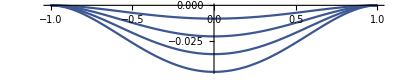

```mathematica
With[
{R=1},
Plot[Table[bendsecond[r,c,R],{c,-3,0,0.8}],{r,-R,R}, AspectRatio->0.2,ColorFunction->([#3]&)]
]
```

The plot shows when pressure is applied  in the disk the plate  starts to  bend, each line represents a different value of pressure and the bending of the plate.

Plots  the bending for the plate with fix ends, keeping radius (R) and constant (c) at fixed values.

```mathematica
With[
{R=1,c=0.3},
RevolutionPlot3D[bendsecond[r,c,R][[1]],{r,-R,R},ColorFunction->([#3]&)]
]
```

-Graphics3D-

## Solving PDE for a thin plate with rectangular shape.

Note : In this solution the  plate constant becomes  s lowercase, and load is the pressure applied to the thin plate.

Load and deflection is assumed to behave  as the following functions :

Clears the value of constant c and d. Defines the load as a  function of constant p and the plate dimensions a and b.

```mathematica
ClearAll[d,c]
load= p*Sin[(Pi*m*x)/a]*Sin[(Pi*n*y)/b]
```

p Sin[(m π x)/a] Sin[(n π y)/b]

and the deflection solution can be assumed  likewise :

Defines the  deflection as a function of constant d, and plate dimensions.

```mathematica
deflection=d*Sin[(Pi*m*x)/a]*Sin[(Pi*n*y)/b]
```

d Sin[(m π x)/a] Sin[(n π y)/b]

Plugging both assumptions in  the  general  equation for plate theory and solving

Solves the general equation in plate theory for the function above.

```mathematica
Laplacian[Laplacian[deflection,{x,y}],{x,y}]
```

(d m^4 π^4 Sin[(m π x)/a] Sin[(n π y)/b])/a^4+(2 d m^2 n^2 π^4 Sin[(m π x)/a] Sin[(n π y)/b])/(a^2 b^2)+(d n^4 π^4 Sin[(m π x)/a] Sin[(n π y)/b])/b^4

The coefficient d is obtained for deflection.

Solves for the constant d from the general equation of plate theory.

```mathematica
coeff1=Solve[Laplacian[Laplacian[deflection,{x,y}],{x,y}]==load/c,d]
```

{{d→(a^4 b^4 p)/(c (b^2 m^2+a^2 n^2)^2 π^4)}}

And replaced into the deflection formula above.

Constant is replaced in the general equation.

```mathematica
deflection=deflection/.coeff1
```

{(a^4 b^4 p Sin[(m π x)/a] Sin[(n π y)/b])/(c (b^2 m^2+a^2 n^2)^2 π^4)}

Fourier analysis can be done for the load , and the  coefficient is obtained :

Fourier analysis to obtain the coefficient p.

```mathematica
coeff2=(4/a*b )*Integrate[Integrate[po*Sin[Pi*m*x/a]*Sin[Pi*n*y/b],{x,0,a}],{y,0,b}]
```

(16 b^2 po Sin[(m π)/2]^2 Sin[(n π)/2]^2)/(m n π^2)

Where po  is the pressure  at which the plate is subjected to.

Last , the coefficients obtained can combine to compute the deflection :

Plugs the value of the constant p into the deflection equation.

```mathematica
deflection=deflection/.p->coeff2
```

{(16 a^4 b^6 po Sin[(m π)/2]^2 Sin[(n π)/2]^2 Sin[(m π x)/a] Sin[(n π y)/b])/(c m n (b^2 m^2+a^2 n^2)^2 π^6)}

For basic analysis  a and b are plate dimensions, c   is the constant define above and  po the pressure applied.

Replaces the value  of constant a,b, c and po in the deflection equation.

```mathematica
deflection=deflection/.{a->1,b->1,c->1,po->1}
```

{(16 Sin[(m π)/2]^2 Sin[(n π)/2]^2 Sin[m π x] Sin[n π y])/(m n (m^2+n^2)^2 π^6)}

Finally the result is plotted for  100 terms, depending on the   computer  the deflection can have more terms for more accurate results. Theoretically the sum should be up to infinity.

Sum m and n in order to obtain the final result of the deflection.

```mathematica
result= Sum[deflection,{m,1,100},{n,1,100}];
```

Plot the surface of the bending plate with fix ends.

```mathematica
Plot3D[result,{x,0,1},{y,0,1},ColorFunction->([#3]&)]
```

-Graphics3D-

## Further explorations

Energy methods for the bending of thin plates

Combined bending and in-plane loading of a thing rectangular plate

The Vibration of Thin Plates by Using Modal Analysis

## Author contact information

jcarabalica@gmail.com

Jorge Carabali Caicedo

Website: www.jorge.engineer